# Figure 6

```mathematica
SetDirectory[NotebookDirectory[]];
```

All data were generated with julia code https : // github . com/djuliannader/RabiModel . git

## Time-dependent term ~σ_z

#### Phase sensitivity

```mathematica
Datfis={{1.4,1.8496498122849574},{1.8,1.8505934887047815},{2,1.8490726520594976},{2.16,1.8059491659279359},{2.17,2.050910986159062},{2.171,2.4098520132203936},{2.172,3.298437030033955},{2.173,3.5102030571196767},{2.174,3.681261552045513},{2.175,2.935939537410965},{2.176,2.544070205623636},{2.177,2.337317480779564},{2.178,2.217155783271115},{2.179,2.1410414605022092},{2.18,2.089467845215173},{2.19,1.933712460767559},{2.2,1.9017950442484914},{2.3,1.8664960385937475},{2.4,1.8639326692699272},{2.6,1.8646713220813504},{2.8,1.8676055593779266},{3,1.871999643574576},{3.2,1.878121586618649},{3.4,1.8867555776942242},{3.6,1.8995347771044053},{3.8,1.9202005117147356},{4,1.959971455501754},{4.05,1.9769119701239874},{4.1,1.9999844628286758},{4.15,2.0344193373051063},{4.2,2.0963696092899555},{4.21,2.127328073625103},{4.22,2.1428023654901818},{4.23,2.2258853680212685},{4.24,2.2292125002925958},{4.25,2.384247128936587},{4.26,2.7014800928611877},{4.27,2.6301940357461886},{4.28,4.481004478220652},{4.29,3.3962900879621967},{4.3,3.1243651487379553},{4.31,3.4372136653003698},{4.32,4.168709991057375},{4.33,2.8833798300909965},{4.34,2.337359526275622},{4.35,2.402373242787396},{4.36,2.9482683291328056},{4.37,2.4172533463404684},{4.38,1.797095781362147},{4.39,1.2854825556686007},{4.4,1.2790291107257277},{4.45,1.9031033658101442},{4.5,1.4217919139162614},{4.55,0.12656382339696487},{4.6,0.8318712123965564},{4.65,1.2313341847643302},{4.7,1.413129572312737},{4.75,1.5118487473316222},{4.8,1.572901426105342},{4.85,1.614151648240974},{4.9,1.643815149702035},{4.95,1.6661459582907179},{5,1.6835529110212906},{5.1,1.7089162700037872},{5.2,1.7264932163209599},{5.4,1.749228743553875},{5.6,1.7632559885481782},{5.8,1.7727308619806796},{6,1.7795180423735204},{6.2,1.7845704038146801},{6.4,1.7883671496376983},{6.6,1.7918081388142084},{6.8,1.7940368046693607},{7,1.7958874541899517},{7.2,1.7973115329495408},{7.4,1.7983287768372753},{7.6,1.7989186797356767},{7.8,1.7989888866274675},{8,1.798297763901672},{8.2,1.796202996251919},{8.4,1.790550928027511},{8.6,1.768087702369015},{8.65,1.749616564191876},{8.7,1.6703619034380972},{8.75,1.1969655948420455},{8.76,2.4316374200275117},{8.768,1.4557571862502476},{8.77,1.77661022694027},{8.78,1.9826997334002845},{8.79,1.9580578493921093},{8.8,1.933160961063201},{8.85,1.87384880286276},{8.9,1.8528873764038005},{9,1.8361554177700403},{9.2,1.8253609265138622},{9.4,1.8215195685502292},{9.6,1.819692235241883}};;
```

```mathematica
exres=8.801011;
Datafisher=Table[{Datfis[[i,1]]/exres,Datfis[[i,2]]},{i,1,Length[Datfis]}];
```

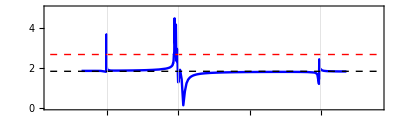

```mathematica
fig4dzoomin=Show[ListPlot[Datafisher,Joined->True,
PlotStyle->{Blue,Thickness[0.0043]},PlotRange->{{0.05,1.2},{0,5}},GridLines->{{0.25,0.5,1},{}},GridLinesStyle->{{Red},{}},Frame->True,LabelStyle->{10,Black}],Plot[2.67,{x,0,1.2},PlotStyle->{Red,Dashed,Thick}],Plot[1.8283437968627987,{x,0,1.2},PlotStyle->{Black,Dashed,Thick}],AspectRatio->0.3,ImageResolution->500]
```

```mathematica
wigner1=Import["wigner_zoomin1.png"];
wigner2=Import["wigner_zoomin2.png"];
wigner3=Import["wigner_zoomin3.png"];
wigner4=Import["wigner_zoomin4.png"];
wigner5=Import["wigner_zoomin5.png"];
wigner6=Import["wigner_zoomin6.png"];
wigner7=Import["wigner_zoomin7.png"];
wigner8=Import["wigner_zoomin8.png"];
wigner9=Import["wigner_zoomin9.png"];
wigner10=Import["wigner_zoomin10.png"];
wigner11=Import["wigner_zoomin11.png"];
wigner12=Import["wigner_zoomin12.png"];
wigner13=Import["wigner_zoomin13.png"];
```

```mathematica
Reswig=Show[fig4dzoomin,Graphics@Inset[wigner1,{0.05,0.3},{Left,Bottom},Scaled[0.3]],Graphics@Inset[wigner2,{0.07,3.2},{Left,Bottom},Scaled[0.3]],Graphics@Inset[wigner3,{0.28,1.94},{Left,Bottom},Scaled[0.3]],Graphics@Inset[wigner4,{0.3,3.2},{Left,Bottom},Scaled[0.3]],Graphics@Inset[wigner5,{0.54,3.4},{Left,Bottom},Scaled[0.3]],Graphics@Inset[wigner6,{0.66,2.8},{Left,Bottom},Scaled[0.3]],Graphics@Inset[wigner7,{0.3,0.09},{Left,Bottom},Scaled[0.3]],Graphics@Inset[wigner8,{0.56,0.1},{Left,Bottom},Scaled[0.3]],Graphics@Inset[wigner9,{0.68,-0.05},{Left,Bottom},Scaled[0.3]],Graphics@Inset[wigner10,{0.8,0.05},{Left,Bottom},Scaled[0.3]],Graphics@Inset[wigner11,{0.8,2.8},{Left,Bottom},Scaled[0.3]],Graphics@Inset[wigner12,{1.02,0.1},{Left,Bottom},Scaled[0.3]],Graphics@Inset[wigner13,{1.02,2.7},{Left,Bottom},Scaled[0.3]],
Graphics[{Thickness[0.002],Arrowheads[0.035],Arrow[{{0.15,1.2},{1.8/exres,1.85}}]}],Graphics[{Thickness[0.002],Arrowheads[0.035],Arrow[{{0.18,3.8},{2.173/exres,3.51}}]}],Graphics[{Thickness[0.002],Arrowheads[0.035],Arrow[{{0.31,2.7},{2.174/exres,3.68}}]}],
Graphics[{Thickness[0.002],Arrowheads[0.035],Arrow[{{0.4,3.9},{4.28/exres,4.4810}}]}],Graphics[{Thickness[0.002],Arrowheads[0.035],Arrow[{{0.57,4.2},{4.31/exres,3.44}}]}],
Graphics[{Thickness[0.002],Arrowheads[0.035],Arrow[{{0.67,3.4},{4.37/exres,2.42}}]}],Graphics[{Thickness[0.002],Arrowheads[0.035],Arrow[{{0.59,0.8},{4.6/exres,0.8319}}]}],
Graphics[{Thickness[0.002],Arrowheads[0.035],Arrow[{{0.9,0.9},{8.75/exres,1.19}}]}],Graphics[{Thickness[0.002],Arrowheads[0.035],Arrow[{{0.41,0.82},{4.4/exres,1.28}}]}],
Graphics[{Thickness[0.002],Arrowheads[0.035],Arrow[{{0.75,1},{6.8/exres,1.794}}]}],
Graphics[{Thickness[0.002],Arrowheads[0.035],Arrow[{{1.05,0.9},{8.768/exres,1.456}}]}],
Graphics[{Thickness[0.002],Arrowheads[0.035],Arrow[{{0.91,3.4},{8.76/exres,2.43}}]}],Graphics[{Thickness[0.002],Arrowheads[0.035],Arrow[{{1.04,3.3},{8.78/exres,1.98}}]}]]
```

-Graphics-

```mathematica
Export["zoominfisher.png",Reswig]
```

zoominfisher.png

#### Displacement sensitivity

```mathematica
Datfisdis={{1.43765,1.5502085500120806},{1.4378,1.3941353854341512},{1.438,1.389162499839122},{1.44,1.3883114118212108},{1.8,1.3908477203292815},{2,1.3927265528529675},{2.16,1.3952822873245212},{2.17,1.4131290983397538},{2.171,1.4391761651152788},{2.172,1.6019800972828946},{2.173,3.7565943374805384},{2.174,1.5107139252854709},{2.175,1.4296262677041454},{2.176,1.4114340867229573},{2.177,1.4045804974139933},{2.178,1.401274557468325},{2.179,1.3994294912807075},{2.18,1.3982956742582475},{2.19,1.3956391813180653},{2.2,1.395381488819788},{2.3,1.3964521508545817},{2.4,1.3979559214073416},{2.6,1.4015744437871198},{2.8,1.4062232833620614},{3,1.4123433609488099},{3.2,1.4206880065747003},{3.4,1.432642963337933},{3.6,1.4510616047971816},{3.8,1.4829080278869753},{4,1.5508871314634258},{4.05,1.5819174063318848},{4.1,1.625291857104569},{4.15,1.6904221231357395},{4.2,1.8003791686550765},{4.21,1.8341851550960278},{4.22,1.870200470070952},{4.23,1.917417827891255},{4.24,1.970709807239547},{4.25,2.0487636776085454},{4.26,2.1306308047816804},{4.27,2.2728421746459126},{4.28,2.9990399138063557},{4.29,2.5403291378531443},{4.3,3.050244418924804},{4.31,6.026694727495723},{4.32,3.001640639391336},{4.33,3.3001424426662274},{4.34,4.708759485131133},{4.35,3.710660018429782},{4.36,2.3516525848573506},{4.37,2.3830383066689054},{4.38,2.8317628696796415},{4.39,3.445794397438575},{4.4,0.9003694991684559},{4.45,0.6577962886547093},{4.5,0.8832128480392878},{4.55,1.0058577384950145},{4.6,1.0790663748486593},{4.65,1.1273286246210836},{4.7,1.1614632305245},{4.75,1.1868589001667298},{4.8,1.206481263970348},{4.85,1.2220928101527055},{4.9,1.2348056418400977},{4.95,1.24535576089102},{5,1.2542495294335918},{5.1,1.2684098623599198},{5.2,1.2791721052682783},{5.4,1.29441945831698},{5.6,1.30466682598768},{5.8,1.311990991367831},{6,1.3174538174738295},{6.2,1.3216530321193136},{6.4,1.3249487202301649},{6.6,1.3275686860283906},{6.8,1.3296588149265214},{7,1.3313136862967165},{7.2,1.3325877525305707},{7.4,1.3335004196004636},{7.6,1.3340301201501525},{7.8,1.3340910520296827},{8,1.3334656835442864},{8.2,1.331587968634119},{8.4,1.3266135666790677},{8.6,1.3078483825253522},{8.65,1.2928186276030331},{8.7,1.2580954107598663},{8.75,1.03250212116051},{8.76,0.787931425211135},{8.768,4.384826777952892},{8.77,3.2204674894715573},{8.78,1.8438639502192937},{8.79,1.6210048351745223},{8.8,1.5347916961373158},{8.85,1.418592158373959},{8.9,1.3906108364466714},{9,1.3710649331059082},{9.2,1.3595072584148529},{9.4,1.3555645723163838},{9.4,1.3537153129501949}};
```

```mathematica
exres=8.801011;
Datafisherdis=Table[{Datfisdis[[i,1]]/exres,Datfisdis[[i,2]]},{i,1,Length[Datfisdis]}];
```

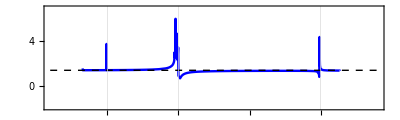

```mathematica
fig5dzoomin=Show[ListPlot[Datafisherdis,Joined->True,
PlotStyle->{Blue,Thickness[0.0043]},PlotRange->{{0.05,1.2},{-2,7}},GridLines->{{0.25,0.5,1},{}},GridLinesStyle->{{Red},{}},Axes->False,Frame->True,LabelStyle->{10,Black}],Plot[1.382118818569585,{x,0,1.2},PlotStyle->{Black,Dashed,Thick}],AspectRatio->0.3,ImageResolution->500]
```

```mathematica
wigner1=Import["wigner_zoomin1.png"];
wigner2=Import["wigner_zoomin2.png"];
wigner3=Import["wigner_zoomin3.png"];
wigner4=Import["wigner_zoomin4.png"];
wigner5=Import["wigner_zoomin5.png"];
wigner6=Import["wigner_zoomin6.png"];
wigner7=Import["wigner_zoomin7.png"];
wigner8=Import["wigner_zoomin8.png"];
wigner9=Import["wigner_zoomin9.png"];
wigner10=Import["wigner_zoomin10.png"];
wigner11=Import["wigner_zoomin11.png"];
wigner12=Import["wigner_zoomin12.png"];
wigner13=Import["wigner_zoomin13.png"];
```

```mathematica
Reswig=Show[fig5dzoomin,Graphics@Inset[wigner1,{0.05,-1.6},{Left,Bottom},Scaled[0.3]],Graphics@Inset[wigner2,{0.06,2.5},{Left,Bottom},Scaled[0.3]],Graphics@Inset[wigner3,{0.28,1.4},{Left,Bottom},Scaled[0.3]],Graphics@Inset[wigner4,{0.3,4},{Left,Bottom},Scaled[0.3]],Graphics@Inset[wigner5,{0.55,4.2},{Left,Bottom},Scaled[0.3]],Graphics@Inset[wigner6,{0.55,1.8},{Left,Bottom},Scaled[0.3]],Graphics@Inset[wigner7,{0.35,-1.8},{Left,Bottom},Scaled[0.3]],Graphics@Inset[wigner8,{0.55,-1.8},{Left,Bottom},Scaled[0.3]],Graphics@Inset[wigner9,{0.67,-2},{Left,Bottom},Scaled[0.3]],Graphics@Inset[wigner10,{0.82,-1.5},{Left,Bottom},Scaled[0.3]],Graphics@Inset[wigner11,{1.02,-1.8},{Left,Bottom},Scaled[0.3]],Graphics@Inset[wigner12,{0.78,3.8},{Left,Bottom},Scaled[0.3]],Graphics@Inset[wigner13,{1.02,2.3},{Left,Bottom},Scaled[0.3]],Graphics[{Thickness[0.002],Arrowheads[0.035],Arrow[{{0.15,0},{1.8/exres,1.39}}]}],Graphics[{Thickness[0.002],Arrowheads[0.035],Arrow[{{0.18,3.8},{2.173/exres,3.757}}]}],Graphics[{Thickness[0.002],Arrowheads[0.035],Arrow[{{0.31,2.4},{2.174/exres,1.51}}]}],
Graphics[{Thickness[0.002],Arrowheads[0.035],Arrow[{{0.4,4.5},{4.28/exres,3}}]}],Graphics[{Thickness[0.002],Arrowheads[0.035],Arrow[{{0.58,5.5},{4.31/exres,6.02}}]}],
Graphics[{Thickness[0.002],Arrowheads[0.035],Arrow[{{0.58,3.2},{4.37/exres,2.38}}]}],Graphics[{Thickness[0.002],Arrowheads[0.035],Arrow[{{0.58,-0.2},{4.6/exres,1.08}}]}],
Graphics[{Thickness[0.002],Arrowheads[0.035],Arrow[{{0.91,0.3},{8.75/exres,1.03}}]}],Graphics[{Thickness[0.002],Arrowheads[0.035],Arrow[{{0.45,0.2},{4.4/exres,0.9}}]}],
Graphics[{Thickness[0.002],Arrowheads[0.035],Arrow[{{0.75,0},{6.8/exres,1.33}}]}],
Graphics[{Thickness[0.002],Arrowheads[0.035],Arrow[{{0.9,5},{8.768/exres,4.38}}]}],
Graphics[{Thickness[0.002],Arrowheads[0.035],Arrow[{{1.05,-0.3},{8.76/exres,0.79}}]}],Graphics[{Thickness[0.002],Arrowheads[0.035],Arrow[{{1.05,3.3},{8.78/exres,1.84}}]}]]
```

-Graphics-

```mathematica
Export["zoominfisher2.png",Reswig]
```

zoominfisher2.png

## Time-dependent term ~σ_x

#### Phase sensitivity

```mathematica
Datfis={{1.2,1.827945139961394},{1.3,1.827802582307606},{1.4,1.8276216069451061},{1.5,1.8273943335068448},{1.6,1.8271119924826016},{1.7,1.8268781120714939},{1.72,1.828171032242086},{1.73,3.4903111858310387},{1.74,1.8285047927174645},{1.8,1.8264339519626802},{1.9,1.8258711620519323},{2,1.8252440097283888},{2.1,1.824495604022407},{2.2,1.8235966995301784},{2.3,1.8225139664658339},{2.4,1.8212057853814148},{2.5,1.8196245158650424},{2.6,1.817757264228411},{2.7,1.8159995779082039},{2.8,1.8208206604306054},{2.82,1.8333015937129475},{2.84,1.8477723678785076},{2.86,1.9167271254507803},{2.88,2.2598946748276387},{2.89,2.3801967716945827},{2.9,2.887925994566505},{2.91,2.9539142783483157},{2.92,2.6265638906344115},{2.94,2.0868768417603354},{2.96,1.9499172591265603},{2.98,1.8985845512554491},{3,1.8735104947664758},{3.1,1.8350494852611074},{3.2,1.824263274204354},{3.3,1.8180651914680552},{3.4,1.8131849229878012},{3.5,1.8086952434598556},{3.6,1.8042258869769},{3.7,1.7995909125128047},{3.8,1.794678371118084},{3.9,1.789408940801298},{4,1.783715196769834},{4.1,1.777519883664639},{4.2,1.7706588451853007},{4.3,1.761782106821137},{4.4,1.7588165594446443},{4.5,1.7494299440651495},{4.6,1.740462614784408},{4.7,1.7310803801677161},{4.8,1.7211789514672764},{4.9,1.7107352165771028},{5,1.6997514953785553},{5.1,1.6882443143217316},{5.2,1.6762438086888807},{5.3,1.663780926864092},{5.4,1.6509087466206418},{5.5,1.637681069384823},{5.6,1.6241614634821289},{5.7,1.6104205299032834},{5.8,1.5965346856780718},{5.9,1.582584762286564},{6,1.5686544347924216},{6.1,1.5548285628737375},{6.2,1.5411915133263216},{6.3,1.5278255640592602},{6.4,1.5148094920043849},{6.5,1.5022174567508009},{6.6,1.4901183036568477},{6.7,1.4785754325809004},{6.8,1.4676474240617141},{6.9,1.4573897051106075},{7,1.447857710791884},{7.1,1.439112330577926},{7.2,1.431229073096387},{7.3,1.4243136711829312},{7.4,1.4185295433390985},{7.5,1.4141485304085117},{7.55,1.4126215572700513},{7.6,1.4116508266613237},{7.65,1.4113633560304355},{7.7,1.4119389593626268},{7.75,1.4136383824681353},{7.8,1.4168511635040066},{7.85,1.422181753970906},{7.9,1.430616020543554},{7.95,1.4438753346440851},{8,1.465277415782811},{8.05,1.502310461273775},{8.1,1.5789043940280034},{8.15,3.1913782399485635},{8.2,7.206369005972193},{8.25,7.957423954082055},{8.3,8.31637430174526},{8.35,0.5147310622555332},{8.4,0.5394753718831249},{8.45,0.5654235145148423},{8.5,0.59258062604927},{8.55,0.6209310438424032},{8.6,0.6504329841164482},{8.65,0.6810130430214637},{8.7,0.7125610475271789},{8.75,0.7449260130856711},{8.8,0.7779141669904657},{8.85,0.8112900845760559},{8.9,0.8447818536312358},{8.95,0.8780907415154728},{9,0.9109050806514896},{9.1,0.9738409243829255},{9.2,1.0314814062701023},{9.4,1.1263798592236538},{9.6,1.1944492922427015},{9.8,1.2417495595788275},{10,1.2749867586371242},{10.2,1.2991140132180767}};
```

```mathematica
exres=8.801011;
Datafisher=Table[{Datfis[[i,1]]/exres,Datfis[[i,2]]},{i,1,Length[Datfis]}];
```

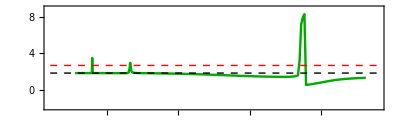

```mathematica
fig4dzoomin=Show[ListPlot[Datafisher,Joined->True,
PlotStyle->{Darker[Green],Thickness[0.0043]},PlotRange->{{0.05,1.2},{-2,9}},Axes->False,GridLines->{{1/5,1/3,1},{}},GridLinesStyle->{{Red},{}},Frame->True,LabelStyle->{10,Black}],Plot[2.67,{x,0,1.2},PlotStyle->{Red,Dashed,Thick}],Plot[1.8283437968627987,{x,0,1.2},PlotStyle->{Black,Dashed,Thick}],AspectRatio->0.3,ImageResolution->500]
```

```mathematica
wigner1=Import["wigner_zoomin1sigx.png"];
wigner2=Import["wigner_zoomin2sigx.png"];
wigner3=Import["wigner_zoomin3sigx.png"];
wigner4=Import["wigner_zoomin4sigx.png"];
wigner5=Import["wigner_zoomin5sigx.png"];
wigner6=Import["wigner_zoomin6sigx.png"];
wigner7=Import["wigner_zoomin7sigx.png"];
wigner8=Import["wigner_zoomin8sigx.png"];
wigner9=Import["wigner_zoomin9sigx.png"];
wigner10=Import["wigner_zoomin10sigx.png"];
```

```mathematica
Reswig=Show[fig4dzoomin,Graphics@Inset[wigner1,{0.05,-2.2},{Left,Bottom},Scaled[0.25]],Graphics@Inset[wigner2,{0.07,5},{Left,Bottom},Scaled[0.25]],Graphics@Inset[wigner3,{0.2,-2.25},{Left,Bottom},Scaled[0.25]],Graphics@Inset[wigner4,{0.2,4.7},{Left,Bottom},Scaled[0.25]],Graphics@Inset[wigner5,{0.37,4.2},{Left,Bottom},Scaled[0.25]],Graphics@Inset[wigner6,{0.52,-2},{Left,Bottom},Scaled[0.25]],Graphics@Inset[wigner7,{0.65,3.2},{Left,Bottom},Scaled[0.25]],Graphics@Inset[wigner8,{0.73,6},{Left,Bottom},Scaled[0.25]],Graphics@Inset[wigner9,{1.01,-2.15},{Left,Bottom},Scaled[0.25]],Graphics@Inset[wigner10,{1.03,4.3},{Left,Bottom},Scaled[0.25]],
Graphics[{Thickness[0.002],Arrowheads[0.035],Arrow[{{0.12,-0.2},{1.3/exres,1.83}}]}],Graphics[{Thickness[0.002],Arrowheads[0.035],Arrow[{{0.14,5.5},{1.73/exres,3.49}}]}],Graphics[{Thickness[0.002],Arrowheads[0.035],Arrow[{{0.26,-0.2},{2.4/exres,1.82}}]}],
Graphics[{Thickness[0.002],Arrowheads[0.035],Arrow[{{0.28,5.0},{2.91/exres,2.95}}]}],Graphics[{Thickness[0.002],Arrowheads[0.035],Arrow[{{0.4,5.0},{2.92/exres,2.63}}]}],Graphics[{Thickness[0.002],Arrowheads[0.035],Arrow[{{0.55,-0.2},{4.5/exres,1.83}}]}],Graphics[{Thickness[0.002],Arrowheads[0.035],Arrow[{{0.75,4.2},{8.15/exres,3.19}}]}],Graphics[{Thickness[0.002],Arrowheads[0.035],Arrow[{{0.85,7.5},{8.25/exres,7.96}}]}],Graphics[{Thickness[0.002],Arrowheads[0.035],Arrow[{{1.09,-0.75},{8.35/exres,0.51}}]}],Graphics[{Thickness[0.002],Arrowheads[0.035],Arrow[{{1.1,4.75},{9.8/exres,1.24}}]}]]
```

-Graphics-

```mathematica
Export["zoominfisher3.png",Reswig]
```

zoominfisher3.png

#### Displacement sensitivity

```mathematica
Datfisdis={{1.2,1.381118627880617},{1.3,1.3811311329929847},{1.4,1.3811439790581435},{1.5,1.3811573279883538},{1.6,1.3811713774225578},{1.7,1.3811896945065334},{1.72,1.3812258466988023},{1.73,1.448087651425328},{1.74,1.3812274500171189},{1.8,1.3812022487572173},{1.9,1.38121803994859},{2,1.3812356233279508},{2.1,1.3812548173221617},{2.2,1.3812761903222086},{2.3,1.3813009232764268},{2.4,1.3813315723829254},{2.5,1.3813744223387079},{2.6,1.3814482072701055},{2.7,1.3816296516665971},{2.8,1.3825284111939673},{2.82,1.3832168785374217},{2.84,1.3845776367331017},{2.86,1.3886473310979033},{2.88,1.4044543810971057},{2.89,1.4331783965778369},{2.9,1.687961731041951},{2.91,2.1737122545186396},{2.92,1.457989060227789},{2.94,1.394578878531916},{2.96,1.3867334781249874},{2.98,1.3843122354787059},{3,1.3832571227357877},{3.1,1.3819307288779863},{3.2,1.3817082563995329},{3.3,1.3816444175645421},{3.4,1.3816272945948136},{3.5,1.3816292187543109},{3.6,1.3816405697301264},{3.7,1.3816572326264076},{3.8,1.3816771701344106},{3.9,1.3816992458080528},{4,1.38172274135019561},{4.1,1.3817471182001113},{4.2,1.3817717019143554},{4.3,1.3817933485550686},{4.4,1.3818328561686648},{4.5,1.3818546646996877},{4.6,1.3818798869334072},{4.7,1.3819053100139762},{4.8,1.3819304000514652},{4.9,1.3819548665507548},{5,1.381978467951609},{5.1,1.3820009719237387},{5.2,1.3820221613566634},{5.3,1.3820417542242671},{5.4,1.3820595539394445},{5.5,1.3820753143466273},{5.6,1.3820888173577948},{5.7,1.3820998774050843},{5.8,1.3821083664338627},{5.9,1.3821142510509306},{6,1.3821176469699403},{6.1,1.382118898631694},{6.2,1.382118695581211},{6.3,1.3821182430857666},{6.4,1.3821195134977524},{6.5,1.382125619131951},{6.6,1.3821413702786485},{6.7,1.3821741192989963},{6.8,1.3822350540257093},{6.9,1.382341210105406},{7,1.3825186588638296},{7.1,1.3828076662740527},{7.2,1.3832712566717824},{7.3,1.3840098698129806},{7.4,1.3851874021918897},{7.5,1.3870796802425496},{7.55,1.3884324695612105},{7.6,1.3901702191875536},{7.65,1.3924187654470241},{7.7,1.3953548540438308},{7.75,1.399232736339043},{7.8,1.4044290932848174},{7.85,1.4115231364722016},{7.9,1.4214496249220052},{7.95,1.4358190312385273},{8,1.457677949580618},{8.05,1.4936988413287369},{8.1,1.5633107334254859},{8.15,2.1640149487928335},{8.2,7.607438739422191},{8.25,16.314561910297183},{8.3,20.547728944454395},{8.35,0.5536974280142639},{8.4,0.5761842539179961},{8.45,0.5997088783926547},{8.5,0.6242932218374345},{8.55,0.6499437846190174},{8.6,0.6766469606102347},{8.65,0.7043639087278025},{8.7,0.7330253190247151},{8.75,0.7625266179833555},{8.8,0.7927243809349082},{8.85,0.8234349001078166},{8.9,0.854435904513898},{8.95,0.885472237822224},{9,0.9162657985390422},{9.1,0.9759821532453671},{9.2,1.0314648820192207},{9.4,1.1243268800466408},{9.6,1.1915776527375481},{9.8,1.2379183358287962},{10,1.2696376426428315},{10.2,1.2916976489482954}};
```

```mathematica
exres=8.801011;
Datafisherdis=Table[{Datfisdis[[i,1]]/exres,Datfisdis[[i,2]]},{i,1,Length[Datfisdis]}];
```

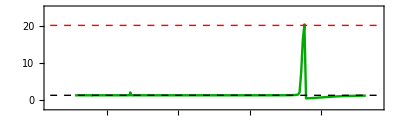

```mathematica
fig5dzoomin=Show[ListPlot[Datafisherdis,Joined->True,
PlotStyle->{Darker[Green],Thickness[0.0043]},PlotRange->{{0.05,1.2},{-2,25}},GridLines->{{1/3,1/5,1},{}},GridLinesStyle->{{Red},{}},Axes->False,Frame->True,LabelStyle->{10,Black}],Plot[1.382118818569585,{x,0,1.2},PlotStyle->{Black,Dashed,Thick}],Plot[20.296888693053788,{
x,0,1.2},PlotStyle->{Red,Dashed,Thick}],AspectRatio->0.3,ImageResolution->500]
```

```mathematica
wigner1=Import["wigner_zoomin1sigx.png"];
wigner2=Import["wigner_zoomin2sigx.png"];
wigner3=Import["wigner_zoomin3sigx.png"];
wigner4=Import["wigner_zoomin4sigx.png"];
wigner5=Import["wigner_zoomin5sigx.png"];
wigner6=Import["wigner_zoomin6sigx.png"];
wigner7=Import["wigner_zoomin7sigx.png"];
wigner8=Import["wigner_zoomin8sigx.png"];
wigner9=Import["wigner_zoomin9sigx.png"];
wigner10=Import["wigner_zoomin10sigx.png"];
```

```mathematica
Reswig=Show[fig5dzoomin,Graphics@Inset[wigner1,{0.035,4.0},{Left,Bottom},Scaled[0.25]],Graphics@Inset[wigner2,{0.06,11.0},{Left,Bottom},Scaled[0.25]],Graphics@Inset[wigner3,{0.21,4.0},{Left,Bottom},Scaled[0.25]],Graphics@Inset[wigner4,{0.21,12.0},{Left,Bottom},Scaled[0.25]],Graphics@Inset[wigner5,{0.34,12.0},{Left,Bottom},Scaled[0.25]],Graphics@Inset[wigner6,{0.45,6.0},{Left,Bottom},Scaled[0.25]],Graphics@Inset[wigner7,{0.7,3.5},{Left,Bottom},Scaled[0.25]],Graphics@Inset[wigner8,{0.73,12},{Left,Bottom},Scaled[0.25]],Graphics@Inset[wigner9,{1.03,12},{Left,Bottom},Scaled[0.25]],Graphics@Inset[wigner10,{1.05,4},{Left,Bottom},Scaled[0.25]],Graphics[{Thickness[0.002],Arrowheads[0.035],Arrow[{{0.12,6},{1.3/exres,1.38}}]}],Graphics[{Thickness[0.002],Arrowheads[0.035],Arrow[{{0.13,13},{1.73/exres,1.45}}]}],Graphics[{Thickness[0.002],Arrowheads[0.035],Arrow[{{0.27,6},{2.4/exres,1.45}}]}],Graphics[{Thickness[0.002],Arrowheads[0.035],Arrow[{{0.28,13},{2.87/exres,2.4}}]}],Graphics[{Thickness[0.002],Arrowheads[0.035],Arrow[{{0.38,14},{2.96/exres,1.9}}]}],Graphics[{Thickness[0.002],Arrowheads[0.035],Arrow[{{0.5,8},{4.5/exres,1.9}}]}],Graphics[{Thickness[0.002],Arrowheads[0.035],Arrow[{{0.8,6},{8.15/exres,2.16}}]}],Graphics[{Thickness[0.002],Arrowheads[0.035],Arrow[{{0.85,16},{8.25/exres,16.31}}]}],Graphics[{Thickness[0.002],Arrowheads[0.035],Arrow[{{1.1,13},{8.35/exres,0.55}}]}],Graphics[{Thickness[0.002],Arrowheads[0.035],Arrow[{{1.12,6},{9.8/exres,1.24}}]}]]
```

-Graphics-

```mathematica
Export["zoominfisher4.png",Reswig]
```

zoominfisher4.png